# Modeling Ionic Currents in Cells

Sam Natarajan, Samion Suwito, Harini Thiagarajan

Within the human body, there are hundreds of trillions of cells, and every cell has hundreds of ion channels in order to transport nutrients and other molecules in and out of the cell. These ion channels are able to function thanks to the ionic currents in cells. However, there are many situations where these ionic channels are disrupted, which can cause major problems in the human body. However, there are certain drugs, such as lidocaine, that have been created to specifically combat these disrupted ionic currents. Our goal in this study was to use mathematical equations to model ion channels and demonstrate the impact of lidocaine in helping those with disrupted ionic currents.

## A Standard Model

Action potentials, which occur when the membrane potential rapidly rises and falls at a specific location, are the result of ion channels located across the cell membrane. During the action potential reaction, these channels selectively choose ions to move down electrochemical gradients, altering the cell’s transmembrane potential. Two ion channel characteristics include selectivity and gating. Selectivity is particularly vital since these channels do not pass through all charged molecules, and these could be extremely selective based on charge. Gating mechanisms determine what causes channels to open.

Cardiac arrhythmia is one example of a medical condition caused by disruptions in ionic currents of ion channels in the human body. This includes either having higher/lower concentrations of these ions on either side of the membrane due to alterations in the selectivity and gating mechanisms. The specific ionic currents that are responsible are sodium, potassium, and leakage (which refers to all the other ionic currents combined), and so we'll focus on them for this study.

### The Hodgkin-Huxley and Nernst Equations

In order to model these ionic currents, we'll use the primary accepted model: a two-gate Hodgkin-Huxley model, where the current is defined by the equation below. Here, g represents the maximal conductance (defined as the ratio of ionic current through the channel to applied voltage), V is the transmembrane potential, and E is the reversal potential for a specific ion. Note that we divide by 100 so as to keep the units the same.

The equation for the Hodgkin-Huxley model:

```mathematica
Icurrent[E_]:=g*(V-E)/100
```

The typical range of the transmembrane potential is from -70 mV to -40 mV, while the value of maximal conductance differs for each type of element (sodium, potassium, and leakage conductance). The values are 120, 36, and .3 for sodium, potassium, and leakage respectively.

In order to determine the reversal potential for each type of ion (sodium, potassium, and leakage), we use the Nernst equation. The Nernst equation (the first equation below) can be used to find the equilibrium potential for the ions present, which can then be substituted into the Hodgkin-Huxley model. When the equation is simplified at normal body temperature [3], we get the second equation below.

The Nernst equation at normal body temperature (where x is the internal ionic concentration and y is the external ionic concentration):

```mathematica
Ek=R*T/zi/F*(Log[(y/x)]);
Ek=-61*Log[10,(x/y)];
```

We can now rewrite our original ionic current equation into one general function as follows:

```mathematica
finalICurrent[g_,int_,ext_]:=g*(V-(-61*Log[10,(int/ext)]))/100
```

By choosing an arbitrary transmembrane potential of -50 mV, we can plot the final current with respect to internal and external concentration. We end up with the visualizations below, which demonstrate sodium, potassium, and leakage respectively.

```mathematica
ICurrent[g_,int_,ext_]:=g*(-50-(-61*Log[10,(int/ext)]));
Column[Plot3D[ICurrent[#,x,y],{x,0,1000},{y,0,1000}]&/@{120,36,.3}]
```

-Graphics3D-
-Graphics3D-
-Graphics3D-

Note that the graphs are all relatively similar in shape. In fact, the biggest difference between the 3 models are simply the value of the ionic current. As shown above, sodium ionic currents have values from -20000 to +10000, potassium ionic currents have values from -6000 to +2000, and leakage ionic currents range from -40 to +20. This means that ionic currents behave rather similarly for all types of ions, and only the values/intensity of these currents vary.

The Animate below models the sodium ionic current for different internal and external concentrations across a range of transmembrane potentials (-70 mV to -40 mV).

```mathematica
Animate[Plot3D[120*(V-(-61*Log[10,(x/y)])),{x,0,1000},{y,0,1000}],{V,-70,-40},SaveDefinitions->True]
```

The Animate below shows how the potassium ionic current changes with respect to different transmembrane potentials.

```mathematica
Animate[Plot3D[36*(V-(-61*Log[10,(x/y)])),{x,0,1000},{y,0,1000}],{V,-70,-40},SaveDefinitions->True]
```

And below is the respective Animate for the leakage ionic current.

```mathematica
Animate[Plot3D[0.3*(V-(-61*Log[10,(x/y)])),{x,0,1000},{y,0,1000}],{V,-70,-40},SaveDefinitions->True]
```

As seen in all the models above, as the transmembrane potential approaches -40 mV (becomes more positive), the values for the sodium, potassium, and leakage ionic currents all decrease. Therefore, it seems that ionic currents decrease in intensity/strength as the transmembrane potential approaches 0.

### The Goldman-Hodgkin-Katz Equation

However, these models are generalized to only one type of ion passing at a time. The Nernst equation assumes that only one ion is present, but in fact, potassium, sodium, and leakage will all be occurring at the same time. To fix this, the Goldman-Hodgkin-Katz equation (GHK) is used to model ionic currents for sodium, potassium, and chloride (which we substitute for leakage) simultaneously.

To use the GHK equation, we first need to initialize a few constants. We create the constants R, T, and F, which represent the universal gas constant, the human body's temperature in Kelvin, and Faraday's constant respectively. Furthermore, we need the permeability— the ease with which ions cross the cell membrane— of sodium, potassium, and chloride.

Initialization of constants:

```mathematica
R=8.3145; (*universal gas constant*)
T=310; (*temperature of normal human body in K*)
F=96485; (*faraday's constant*)

pk=1;(*permeability of potassium*)
pna=0.04;(*permeability of sodium*)
pcl=0.4;(*permeability of chloride*)
```

The GHK equation:

```mathematica
EM[extk_,extna_,extcl_,intk_,intna_,intcl_]:=(R*T/F)*Log[(pk*extk+pna*extna+pcl*extcl)/(pk*intk+pna*intna+pcl*intcl)]
```

Not only does the GHK equation include the constants named above, it also requires the external and internal ionic concentrations of sodium, potassium, and chloride. We were able to find set correspondences for each ion's external and internal concentrations. Specifically, for sodium concentrations, the ratio of external to internal ionic concentrations was 14:1 (14 NA^+ions external per 1 NA^+ ion internal).For potassium, the ratio was 1:30 (external:internal) and for chloride, the ratio was 4:1 (external:internal).

Armed with the GHK equation and the necessary concentrations, we graph all possible membrane potentials to observe a pattern, if any. We create a table of all the membrane potentials based on internal and external concentrations of sodium, potassium, and chloride ions ranging from 1 to 1000 M (steps of 100).

A Table of all possible membrane potentials for various internal and external ionic concentrations:

```mathematica
ems=Table[EM[extk,extna,extcl,extk*30,extna/14,extcl/4],{extk,1,1000,100},{extna,1,1000,100},{extcl,1,1000,100}];
```

We then plot these results. Specifically, we set the difference between external and internal concentrations of all ions (all external - all internal) on the x-axis and the membrane potential on the y-axis.

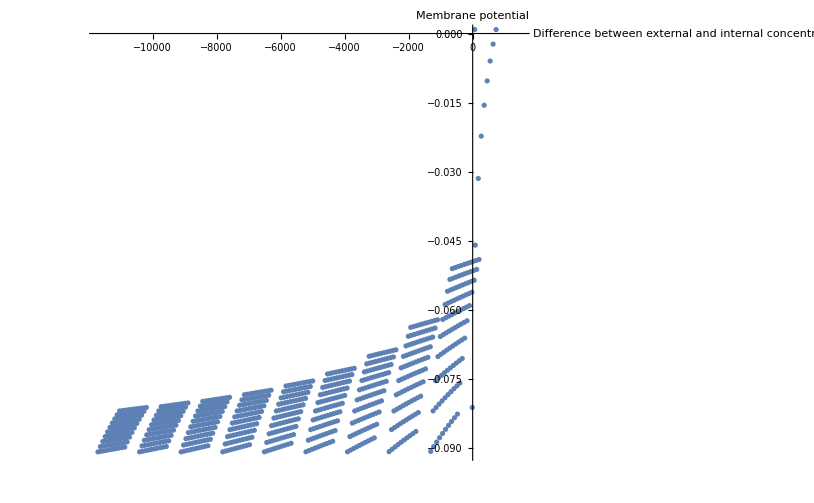

```mathematica
deltas=Table[(extk+extna+extcl)-(extk*14+extna/14+extcl/4),{extk,1,1000,100},{extna,1,1000,100},{extcl,1,1000,100}];
ListPlot[Partition[Riffle[Flatten[deltas],Flatten[ems]],2],AxesLabel->{"Difference between external and internal concentration","Membrane potential"}]
```

The graph above demonstrates the difference in external and internal concentration in a cell (for sodium, potassium, and chloride ions) versus possible membrane potentials. There is a general upward trend, meaning that as the concentration difference becomes smaller (the same external and internal concentration of ions), membrane potentials are less negative.

Combining all the equations above with the Hodgkin-Huxley model, we reach one of the greatest mathematical results in physiology—an equation by Hodgkin and Huxley which was awarded the Nobel Prize in 1963 [6].

The final equation by Hodgkin and Huxley to model ionic currents:

```mathematica
Iionf[V_]:=(-gk(V-Vk)-gna(V-Vna)-gl(V-Vl))/100
```

The equation above is ultimately a combination of the Hodgkin-Huxley model for sodium, potassium, and leakage ionic currents. In order to evaluate it, we needed to label the necessary constants. Note that gk, gna, and gl are the conductances for potassium, sodium, and leakage respectively, and Vk, Vna, and Vl are the reversal potentials for potassium, sodium, and leakage respectively.

The necessary constants for the final equation:

```mathematica
gk=36;
gna=120;
gl=0.3;
Vk=-77;
Vna=50;
Vl=-54.402;
```

Now that we have this, we can graph the ionic currents for an entire cell with respect to the transmembrane potential. The range for V (the transmembrane potential) is between -70 and -40, giving us the graph below.

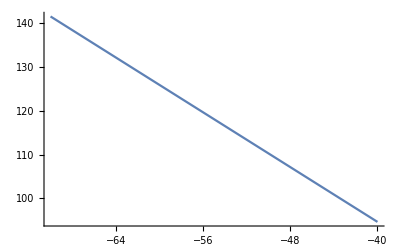

```mathematica
Plot[Iionf[V],{V,-70,-40}]
```

When we graph ionic currents for a transmembrane potential from -80 to -20 mV, we get a linear function, which is in accordance with the linearity of the Hodgkin-Huxley model, as desired.

## The Effect of Lidocaine

### Lidocaine

The first part of our project was devoted to creating a standard model of ionic currents, but the second part is about lidocaine— a specific drug created to combat disrupted ionic currents— and demonstrating its effect.

But what exactly is lidocaine? Lidocaine is a class 1B antiarrhythmic drug made to help those with cardiac arrhythmia, which is a heart problem caused by disrupted ionic currents. Lidocaine has fast unbinding kinetics and keeps the duration of the human action potential the same.

Specifically, lidocaine binds to and blocks the fast sodium channels that occur during the cardiac action potential in order to prevent the balance of ionic currents in the human body from being disturbed. However, lidocaine is one of the safest sodium channel blockers available because it doesn't increase the probability of ventricular arrhythmias [1].

### Equations for Cardiac Sodium Channels

Since lidocaine only blocks sodium channels, we don't need to model the other ion channels. Cardiac sodium channels can be modeled by a subversion of the Hodgkin-Huxley equation, as seen below, where V is the transmembrane potential, Ena is the sodium reversal potential, gna is the maximal conductance, and f is the fraction of channels that are open and unblocked. Note that we divide by 100 to keep constant units of A/m^2.

Equation to model cardiac sodium channels:

```mathematica
Ina=gna(V-Ena)*f/100;
```

Also, since Ena is just the sodium reversal potential, it's constant and equal to 60 mV, and gna is equal to 120, as found in the first part of this project.

Value of Ena and gna:

```mathematica
Ena=60;
gna=120;
```

However, how can we describe f? As based in the Hodgkin-Huxley model, we can say that f = m^3*h since there are 3 activation gates and 1 inactivation gate in a sodium ion channel. Furthermore, since we want to model the change in ionic currents with respect to time, we need to know how the values of m and h change with respect to time. The differential equations that govern the changes in m and h over time are shown below, where alphaM, betaM, alphaH, and betaH are simply voltage-dependent rate constants.

Differential equations for m and h over time:

```mathematica
dmdt=alphaM(1-m)-betaM;
dhdt=alphaH(1-h)-betaH;
```

If we account for the presence of lidocaine, the equation for f changes to include another term involving the variable b, where b is the fraction of channels bound to neutral lidocaine.

Equation for the fraction of open and unblocked channels in the presence of lidocaine:

```mathematica
f=m^3*h*(1-b);
```

Since we have differential equations for m and h, we need a differential equation to express the change in the fraction of channels bound to lidocaine over time (in other words, the change in b with respect to time).

Differential equation for b over time:

```mathematica
dbdt=250(1-h)(1-b)-1.7*10^(-3)b;
```

Furthermore, the value of the maximal conductance (gna) of our model of ionic currents changes in the presence of lidocaine. Specifically, it is the equation seen below, found from combining the differential equations for m, h, and b. We use gnaL to denote the maximal conductance when lidocaine is present.

Conductance for a sodium channel that has lidocaine:

```mathematica
gnaL=gna*m^3*h(1-b);
```

If we combine all these expressions together with the Hodgkin-Huxley model, we get a final equation that expresses the ionic current of a sodium channel in the presence of lidocaine. Note that we use the new expression for gnaL and the expression for f that accounts for lidocaine.

Final equation for ionic current of a sodium channel in the presence of lidocaine:

```mathematica
InaL=gnaL*(V-Ena)*f/100
```

6/5 (1-b)^2 h^2 m^6 (-60+V)

Note that this model was heavily based on the low-dimensional model created by Docken, Clancy, and Lewis [1].

By taking the derivative of the equation above with respect to time, we can see how the ionic currents in sodium channels change over time in the presence of lidocaine. We can then compare this to our standard model of the ionic current in a sodium channel.

When taking the derivative, note that we will take the total derivative with respect to time. This will leave us with some partial derivatives (Dt[m,t], Dt[h,t], and Dt[b,t]) for the changes in m, h, and b respectively over time, which we have expressions for above. The term Dt[V,t] is the change in transmembrane potential over time; however, in the interest of reducing complexity, we will assume that the transmembrane potential will hold constant and thus set Dt[V,t] equal to 0.

```mathematica
Dt[(gnaL*(V-Ena)*(m^3*h)(1-b))/100,t]
```

-12/5 (1-b) h^2 m^6 (-60+V) Dt[b,t]+12/5 (1-b)^2 h m^6 (-60+V) Dt[h,t]+36/5 (1-b)^2 h^2 m^5 (-60+V) Dt[m,t]+6/5 (1-b)^2 h^2 m^6 Dt[V,t]

Rewriting this, we get:

```mathematica
-12/5 (1-b) h^2 m^6 (-60+V)*dbdt+12/5 (1-b)^2 h m^6 (-60+V)*dhdt+36/5 (1-b)^2 h^2 m^5 (-60+V)*dmdt+6/5 (1-b)^2 h^2 m^6*0
```

36/5 (1-b)^2 h^2 (-betaM+alphaM (1-m)) m^5 (-60+V)+12/5 (1-b)^2 (-betaH+alphaH (1-h)) h m^6 (-60+V)-12/5 (1-b) (-0.0017 b+250 (1-b) (1-h)) h^2 m^6 (-60+V)

We did some research  into the values of alphaM, betaM, alphaH, and betaH, and found equations for them [5] in terms of V (which is the transmembrane potential in the presence of lidocaine at 37°C).

Values for alphaM, betaM, alphaH, and betaH:

```mathematica
alphaM=45.43E^(V/13.78);
betaM=0.6628E^(V/-23.25);
alphaH=(6.169*10^(-5))*E^(V/-9.328);
betaH=14.15E^(V/14.91);
```

Therefore, our final equation for the change in ionic currents of sodium channels with lidocaine present with respect to time (dInaLdt) looks like this:

```mathematica
dInaLdt=Simplify[-12/5 (1-b) h^2 m^6 (-60+V)*dbdt+12/5 (1-b)^2 h m^6 (-60+V)*dhdt+36/5 (1-b)^2 h^2 m^5 (-60+V)*dmdt]
```

12/5 (1-b) h m^5 (14.15 (-1.+b) ⅇ^(-0.107204 V) (-4.35972×10^-6+1. ⅇ^(0.174273 V)+4.35972×10^-6 h) m-250. (1.+b (-1.00001+h)-1. h) h m+136.29 (-1.+b) ⅇ^(-0.0430108 V) h (0.0145895+ⅇ^(0.11558 V) (-1.+1. m))) (-60+V)

### Ionic Current Models (with Lidocaine)

Now that we have an equation to represent our final model, we can now model it to visualize lidocaine's impact on ionic currents inside sodium ion channels.

The terms m, h, and b in our equation represent the fraction of activation gates that are open, the fraction of inactivation gates that are open, and the fraction of channels bound to neutral lidocaine respectively. These terms are dependent on the amount of lidocaine introduced to a person's system as well as other details. We refrain from defining equations to govern these variables since that would consist of rather complex equations that require 13 other parameters. Unfortunately, that means we cannot directly model the equation above with a 3D plot. While a Manipulate/Animate could be used, we would not be able to see how these variables change when the membrane potential changes. Therefore, our solution is to model it indirectly.

To do this, we first will relate m, h, and b into one variable. We know that

```mathematica
f=m^3*h*(1-b)
```

(1-b) h m^3

and f ranges from 0 to 1 since m, h, and b all range from 0 to 1. We can use the derivative to find out how f changes with respect to time. Note that f represents the total fraction of channels that are open and unblocked.

```mathematica
Dt[f,t]
```

-h m^3 Dt[b,t]+(1-b) m^3 Dt[h,t]+3 (1-b) h m^2 Dt[m,t]

We can then replace the Dt[b, t], Dt[h, t], and Dt[m, t] with the respective expressions found in the above section.

```mathematica
dfdt=-h m^3 *dbdt+(1-b) m^3 *dhdt+3 (1-b) h m^2 *dmdt
```

3 (1-b) h (-0.6628 ⅇ^(-0.0430108 V)+45.43 ⅇ^(0.0725689 V) (1-m)) m^2+(1-b) (-14.15 ⅇ^(0.0670691 V)+0.00006169 ⅇ^(-0.107204 V) (1-h)) m^3-(-0.0017 b+250 (1-b) (1-h)) h m^3

This still leaves us with 4 variables to deal with. In the interest of simplicity, we will say that the transmembrane potential is -50 mV, which gives us the following values for alphaM, betaM, alphaH, and betaH.

Values for alphaM, betaM, alphaH, and betaH when V = -50 mV:

```mathematica
alphaM50=45.43E^(-50/13.78);
betaM50=0.6628E^(-50/-23.25);
alphaH50=(6.169*10^(-5))*E^(-50/-9.328);
betaH50=14.15E^(-50/14.91);
```

We can use these values in the expressions (dmdt, dhdt, dbdt) for the change in m, h, and b with respect to time when the transmembrane potential is -50 mV.

Differential equations for m, h, and b when V = -50 mV:

```mathematica
dmdt50=alphaM50(1-m)-betaM50;
dhdt50=alphaH50(1-m)-betaH50;
dbdt50=250(1-h)(1-b)-1.7*10^(-3)b;
```

If we use these expressions instead for finding the derivative of f with respect to time, we end up with the following equation.

```mathematica
dfdt=-h m^3 *dbdt50+(1-b) m^3 *dhdt50+3 (1-b) h m^2 *dmdt50
```

3 (1-b) h (-5.6931+1.2065 (1-m)) m^2-(-0.0017 b+250 (1-b) (1-h)) h m^3+(1-b) (-0.494732+0.0131257 (1-m)) m^3

With this, we can model the exact relationship between the value of f and the values of m, h, and b.

First, the Animate below shows how f, the fraction of gates open and unblocked, is related to the values of m, h, and b. Specifically, the model shows that f approaches its maximum as m and h are close to 1, and that f decreases as b increases.

```mathematica
Animate[Plot3D[m^3*h*(1-b),{m,0,1},{h,0,1}],{b,0,1},SaveDefinitions->True]
```

This next Animate demonstrates the change in the fraction of gates open and unblocked with respect to time, based on how m, h, and b change with respect to time. We see that f has a large negative rate of change when m is close to 1 and h is approximately 0.5. Furthermore, f has a rate of change close to 0 when m is close to 0, but as more and more channels are bound to neutral lidocaine, f has a lower rate of change.

```mathematica
Animate[Plot3D[(-h*m^3*(-0.0017b+250(1-b)(1-h))+(1-b)*m^3*(-.494732+.0131257(1-m))+3(1-b)*h*m^2*(-5.6931+1.2065(1-m))),{m,0,1},{h,0,1}],{b,0,1},SaveDefinitions->True]
```

Since the ionic current also depends on the maximal conductance, we turn our attention to the equation below, which ranges from 0 to 120.

```mathematica
gnaL=gna*m^3*h(1-b)
```

120 (1-b) h m^3

By taking the derivative and substituting in the appropriate expressions for Dt[b, t], Dt[h, t], and Dt[m, t], we find how gnaL changes with respect to time. Note this is at a transmembrane potential of -50 mV.

```mathematica
Dt[gnaL,t]
```

-120 h m^3 Dt[b,t]+120 (1-b) m^3 Dt[h,t]+360 (1-b) h m^2 Dt[m,t]

```mathematica
-120 h m^3 *dbdt50+120 (1-b) m^3 *dhdt50+360 (1-b) h m^2 *dmdt50
```

360 (1-b) h (-5.6931+1.2065 (1-m)) m^2-120 (-0.0017 b+250 (1-b) (1-h)) h m^3+120 (1-b) (-0.494732+0.0131257 (1-m)) m^3

With this, we can use an Animate to model the conductance of a cell that contains lidocaine as m, h, and b change.

```mathematica
Animate[Plot3D[gna*m^3*h (1-b)/100,{m,0,1},{h,0,1}],{b,0,1},SaveDefinitions->True]
```

Again, we see that the conductance approaches its maximum value when m and h are close to 1 and decreases in value as b approaches 1.

Using the derivative equation, we use another Animate to show how the conductance of a cell with lidocaine changes over time as m, h, and b change with respect to time.

```mathematica
Animate[Plot3D[(360 (1-b) h (-5.6931041316718565+1.2065024721390372 (1-m)) m^2-120 (-0.0017 b+250 (1-b) (1-h)) h m^3+120 (1-b) (-0.4947318236687685+0.013125703356957355 (1-m)) m^3),{m,0,1},{h,0,1}],{b,0,1},SaveDefinitions->True]
```

Similar to the model for f, we see that the conductance decreases very quickly when m  is close to 1 and h is approximately 0.5. Furthermore, as b increases, the rate of change of conductance decreases.

To summarize our results so far, we have found that the fraction of channels bound to lidocaine and the conductance of a cell when exposed to lidocaine behave rather similarly. They both have maximum values when the fraction of open activation and inactivation gates is close to 1 and seem to decrease at a slower rate when the fraction of channels bound to lidocaine decreases.

Since the ionic current is dependent on both the conductance and the fraction of open channels bound to lidocaine, we predict that the model for the ionic current will be rather similar to this one.

Now, we can return to the original equation for ionic current found above. We have the two equations (the ionic current and the change in the ionic current over time) below.

```mathematica
InaL
```

6/5 (1-b)^2 h^2 m^6 (-60+V)

```mathematica
dInaLdt
```

12/5 (1-b) h m^5 (14.15 (-1.+b) ⅇ^(-0.107204 V) (-4.35972×10^-6+1. ⅇ^(0.174273 V)+4.35972×10^-6 h) m-250. (1.+b (-1.00001+h)-1. h) h m+136.29 (-1.+b) ⅇ^(-0.0430108 V) h (0.0145895+ⅇ^(0.11558 V) (-1.+1. m))) (-60+V)

Again, we assume that the transmembrane potential is equal to -50 mV and simplify the equations above.

```mathematica
V=-50;
Simplify[InaL]
```

-132 (-1+b)^2 h^2 m^6

```mathematica
Simplify[dInaLdt]
```

-66000. (-1.+b) h m^5 ((0.00192642-0.00192642 b) m+(-1.+1. b) h^2 m+h (0.0538392+b (-0.0538392-1.01454 m)+1.01453 m))

We can then use an Animate to show the sodium ionic current in the presence of lidocaine as m, h, and b change.

```mathematica
Animate[Plot3D[(132 (-1+b)^2 h^2 m^6),{m,0,1},{h,0,1}],{b,0,1},SaveDefinitions->True]
```

We can also use a Plot3D to show the sodium ionic current with respect to sodium conductance and the fraction of open and unblocked gates.

```mathematica
Plot3D[(gnaL*(V-60)*f),{f,0,1},{gnaL,0,120}]
```

-Graphics3D-

We see that the sodium ionic current is at its maximum value when the fraction of open and unblocked gates and the sodium conductance is close to 0. Furthermore, we see from the first Animate that the model for sodium ionic current is similar to the models for f and gnaL, as expected. When the fraction of activation and inactivation gates is close to 1, the sodium ionic current is at its maximum; as the fraction of bound lidocaine increases, the sodium ionic current decreases.

Furthermore, modeling the second equation gives us the change in the sodium ionic current in the presence of lidocaine over time, based on how m, h, and b change over time.

```mathematica
Animate[Plot3D[(-66000. (-1.+b) h m^5 ((0.0019264244812472432-0.0019264244812472432 b) m+(-1.+1. b) h^2 m+h (0.05383921991439382+b (-0.05383921991439382-1.0145373324790963 m)+1.0145305324790963 m))),{m,0,1},{h,0,1}],{b,0,1},SaveDefinitions->True]
```

From this, we see that the sodium ionic current increases the fastest when m and h are close to 1, and its maximum rate of change decreases as b increases.

Ultimately, the models show what we expected from the presence of lidocaine. We see that the sodium ionic current decreases as the fraction of channels bound to lidocaine increases, meaning that lidocaine does indeed block sodium channels from having high ionic currents. Furthermore, the sodium ionic current reaches its maximum values when almost all activation gates and inactivation gates are open (m and h are close to 1), which does make sense. Finally, the models also indicate that the sodium ionic current is at its maximum value when the fraction of open and unblocked gates in the presence of lidocaine (dependent on m, h, and b) and the maximal conductance are close to 0. This reinforces our conclusion that lidocaine blocks sodium channels and thus lowers the sodium ionic current, making it a powerful pharmaceutical drug.

Finally, we can directly compare sodium ionic currents with and without lidocaine. To do so, we can graph the standard model and this one side by side.

The equation for the standard model, as found in the part above, is dependent on sodium, potassium, and leakage ionic currents, but we can isolate just the sodium channel.

Sodium ionic current for the standard model:

```mathematica
InaStandard[V_]:=-gna*(V-60)/100
```

Note that we divide by 100 to ensure the units remain constant throughout this study.

Next, we take the equation for the sodium ionic current in the presence of lidocaine, which includes the f term.

Sodium ionic current in the presence of lidocaine:

```mathematica
InaLidocaine[V_]:=-gnaL(V-60)*f/100;
```

Instead of modeling this with a Plot3D and Animate, we'll just set the values of m, h, and b equal to arbitrary values and use that to calculate f and gnaL.

Arbitrary values for m, h, and b to calculate f and gnaL:

```mathematica
m=.8;
h=.8;
b=.2;
gnaL=120*m^3*h*(1-b);
f=m^3*h*(1-b);
```

We finally plot these two functions as the transmembrane potential ranges from -80 to -20 mV.

```mathematica
Plot[{InaStandard[V],InaLidocaine[V]},{V,-80,-20},PlotLabels->{"Without Lidocaine","With Lidocaine"}]
```

-Graphics-

Clearly, lidocaine is an efficient blocker for sodium ion channels— we can clearly see how much lower the sodium ionic current is with lidocaine than without lidocaine.

## Conclusion

Ultimately, our goal for this study was to model ionic currents with mathematical equations and to demonstrate lidocaine's impact on sodium ionic currents. In the first part of the project, we went through the many equations used to create a final standard model for ionic currents, such as the Nernst equation and the Hodgkin-Huxley model. In the second part of the project, we explained the equations for ionic currents in the presence of lidocaine and modeled them to show how lidocaine interacts with sodium ion channels. In the end, we demonstrated that lidocaine is a powerful blocker for sodium ion channels since it's able to decrease the ionic current rather significantly.

### Future Work

We're very proud of all we accomplished!

In the future, we'd like to use this model for other pharmaceutical drugs that impact ionic currents in ion channels. For example, ibogaine is an anti-addiction drug that inhibits voltage-gated ionic currents, and it'd be interesting to modify this model to see how ibogaine works and its impact. Furthermore, we're interested in creating an interactive display of how lidocaine works. Now that we have equations to model its impact on ionic currents, we want to create a visualization that shows exactly how the presence of lidocaine changes ionic currents for many cells in a tissue.

Finally, special thanks to Eryn, our mentor for this project, and Rory, the leader of the entire WELP program!

## References

1. Docken, Steffen S., Clancy, Colleen E., Lewis, Timothy J. “Rate-dependent effects of lidocaine on cardiac dynamics: Development and analysis of a low-dimensional drug-channel interaction model." Public Library of Science, 2021.

2. Grant, Augustus O. "Cardiac Ion Channels." Circulation: Arrhythmia and Electrophysiology, vol. 2, no. 2, 2009, pp 185-194.

3. Klabunde, Richard E. "Cardiac electrophysiology: normal and ischemic ionic currents and the ECG." Advances in Psychology Education, vol. 41, no. 1, 2017, pp 29-37.

4. "Lidocaine." Wikipedia, 25 Dec 2022, https://en.wikipedia.org/wiki/Lidocaine. Accessed 2 Jan. 2022.

5. Mitsuiye T, Noma, A. "Quantification of exponential Na+ current activation in N-bromoacetamide-treated cardiac myocytes of guinea-pig." The Journal of Physiology, vol. 465, no. 1, 1993, pp 245-263.

6. Tuszynski, J.A., Winter, P., White, D. et al. Mathematical and computational modeling in biology at multiple scales. Theor Biol Med Model 11, 52 (2014). https://doi.org/10.1186/1742-4682-11-52.